```mathematica
data1 = Import["/net/home/f09/bajennissen/research/DAY187/tau_day_data/368nm.dat"];
data1hour=Drop[data1, None,1];
data2 = Import["/net/home/f09/bajennissen/research/DAY187/tau_day_data/412nm.dat"];
data2hour=Drop[data2,None,1];
data3 = Import["/net/home/f09/bajennissen/research/DAY187/tau_day_data/500nm.dat"];
data3hour=Drop[data3,None,1];
data4 = Import["/net/home/f09/bajennissen/research/DAY187/tau_day_data/610nm.dat"];
data4hour=Drop[data4,None,1];
data5 = Import["/net/home/f09/bajennissen/research/DAY187/tau_day_data/675nm.dat"];
data5hour=Drop[data5,None,1];
data6= Import["/net/home/f09/bajennissen/research/DAY187/tau_day_data/778nm.dat"];
data6hour=Drop[data6,None,1];
data7 = Import["/net/home/f09/bajennissen/research/DAY187/tau_day_data/862nm.dat"];
data7hour=Drop[data7,None,1];
```

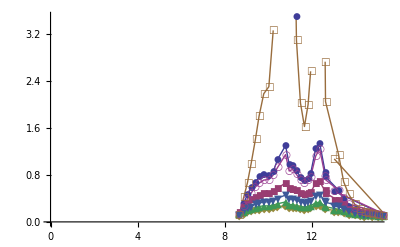

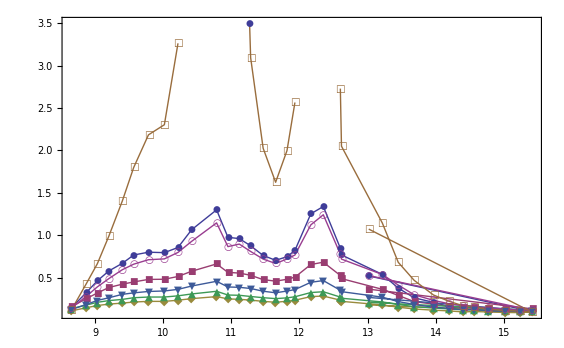

```mathematica
DataPlot=ListPlot[{data1hour,data2hour,data3hour,data4hour,data5hour,data6hour,data7hour}, PlotStyle->PointSize[0.02],PlotMarkers->Automatic,Joined->True,PlotRange->{{0,15},{0,3.5}}]
Show[DataPlot,PlotRange->All,Frame->True, AxesOrigin-> {4,0}]
```